```mathematica
dataUpTo7=Import[FileNameJoin[{NotebookDirectory[],"data",ToString[#]<>"-points.csv"}]]&/@Range[1,7]
```

```mathematica
plotFacetVert[data_,dim_]:=Show[Plot[(2^(dim+1)×dim)/x,{x,1,2^(dim+1)},PlotRange->All,PlotStyle->{LightBlue,Dashed}],ListPlot[data,PlotStyle->{PointSize[0.01],Yellow},AxesOrigin->{0,0}],PlotRange->{{0,2^dim+2},{0,2^dim+2}},AspectRatio->1,AxesOrigin->{0,0},AxesStyle->{{Bold,White},{Bold,White}},AxesLabel->(Style[#,White,Background->Black]&/@{"Facets","Vertices"}),GridLines->Automatic,GridLinesStyle->Gray,Background->Black,PlotLabel->Style["Facets and vertices of 2-level polytopes in dim "<>ToString[dim],White,Background->Black],ImageSize->600]
```

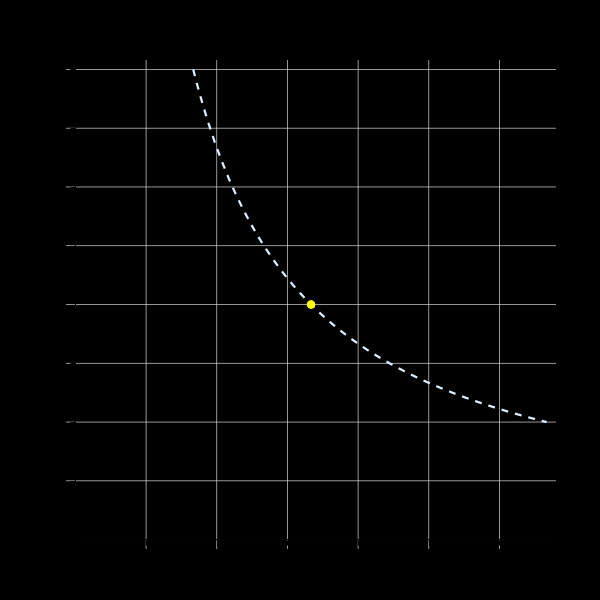
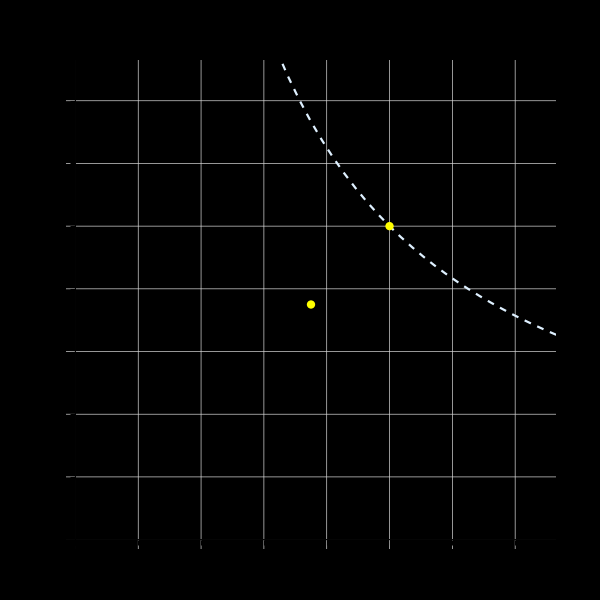
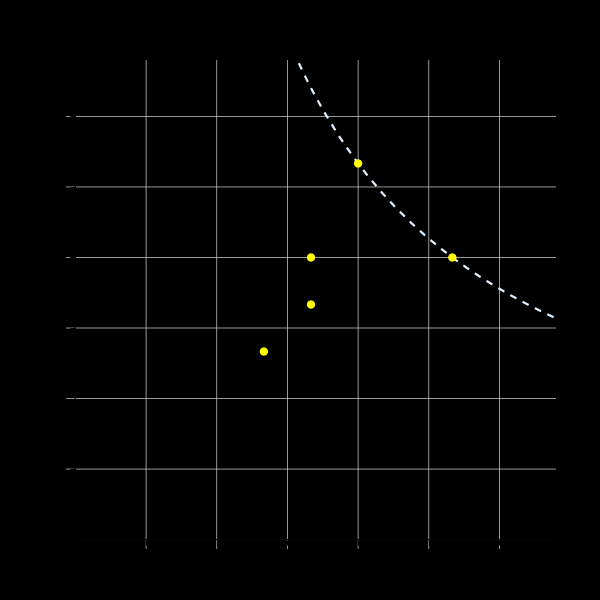
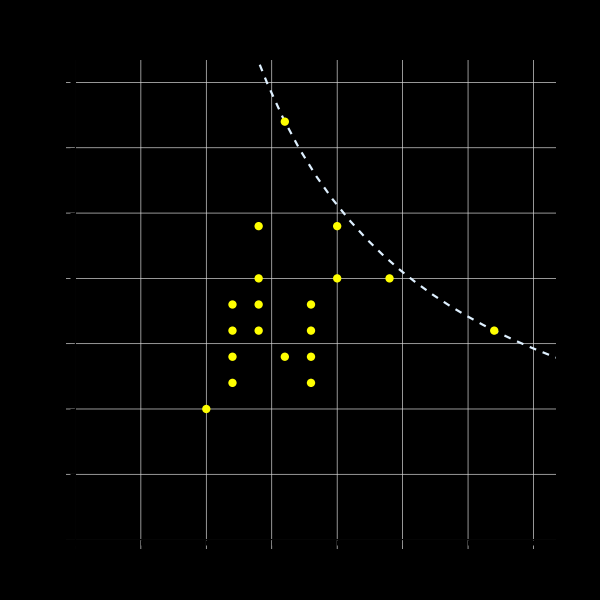
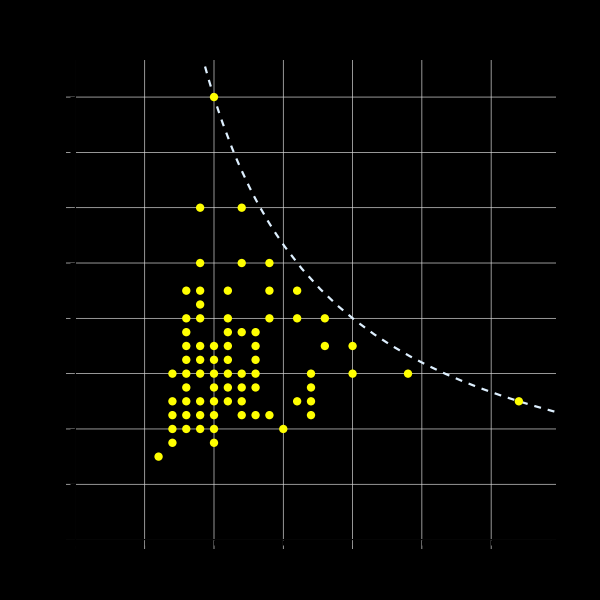
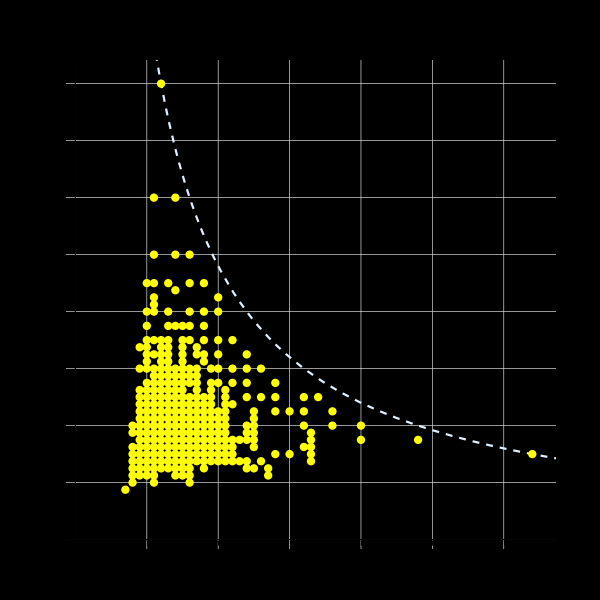
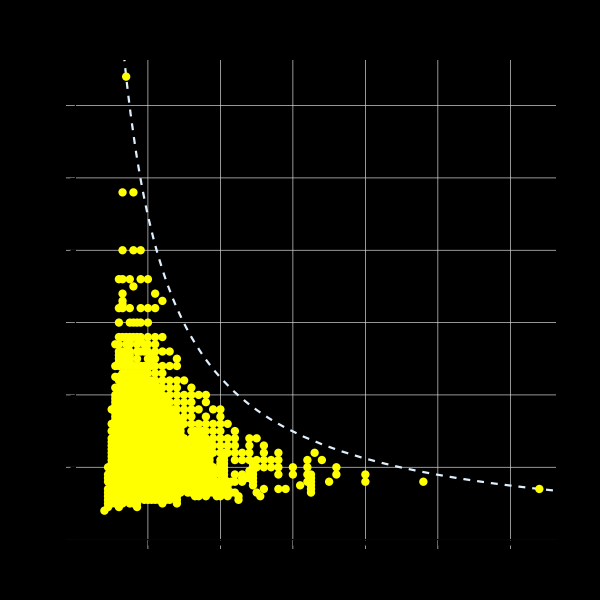
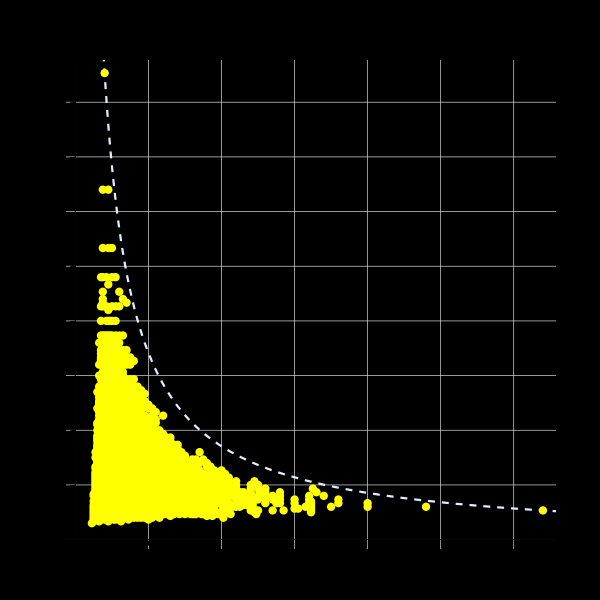

```mathematica
MapIndexed[plotFacetVert[#1,#2[[1]]]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-vert-facet-plots-"<>ToString[#2[[1]]]<>".jpg"}],#1]&,%];
```

```mathematica
points8=Import[FileNameJoin[{NotebookDirectory[],"data","8-points.csv"}]];
```

```mathematica
facetVertData=DeleteDuplicates/@Join[dataUpTo7,{points8}];
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"data","facet-vert-data-1to8.mx"}],facetVertData];
```

```mathematica
minProdData=DeleteDuplicates/@Map[{Min[#],#[[1]]#[[2]]}&,facetVertData,{2}];
maxProdData=DeleteDuplicates/@Map[{Max[#],#[[1]]#[[2]]}&,facetVertData,{2}];
```

```mathematica
vertProdData=DeleteDuplicates/@Map[{#[[2]],#[[1]]#[[2]]}&,facetVertData,{2}];
splitmaxProdData=DeleteDuplicates/@Map[{If[#[[1]]>#[[2]],#[[1]],-#[[2]]],#[[1]]#[[2]]}&,facetVertData,{2}];
```

```mathematica
fvdifProdData=Map[{#[[1]]-#[[2]],#[[1]]#[[2]]}&,facetVertData,{2}];
```

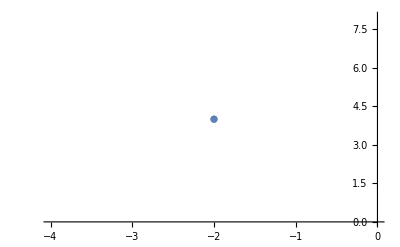
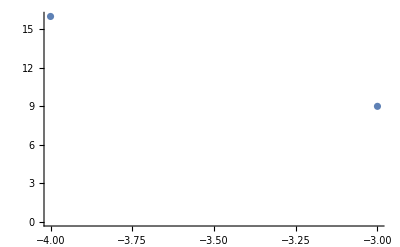
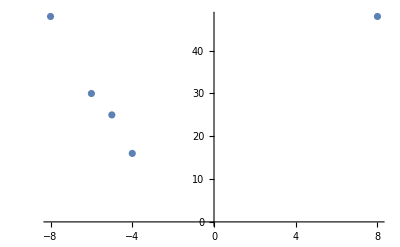
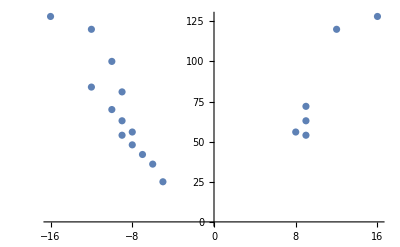
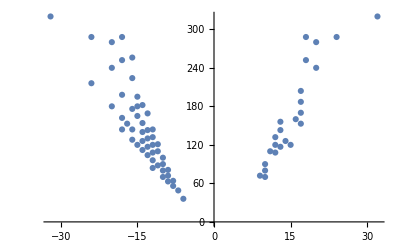
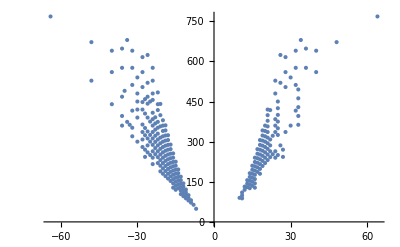
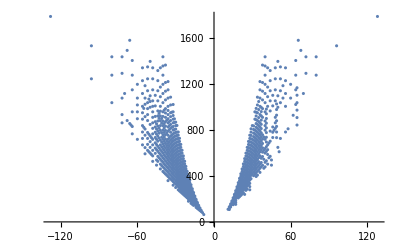
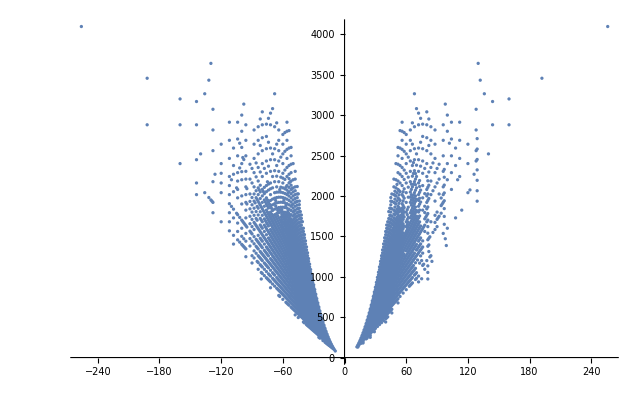

```mathematica
ListPlot[#,PlotRange->All,AxesOrigin->{0,0}]&/@splitmaxProdData
```

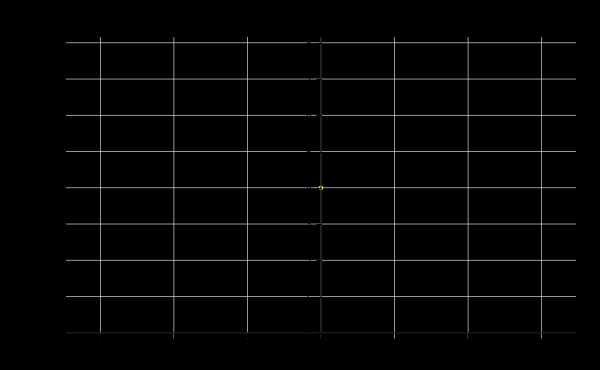
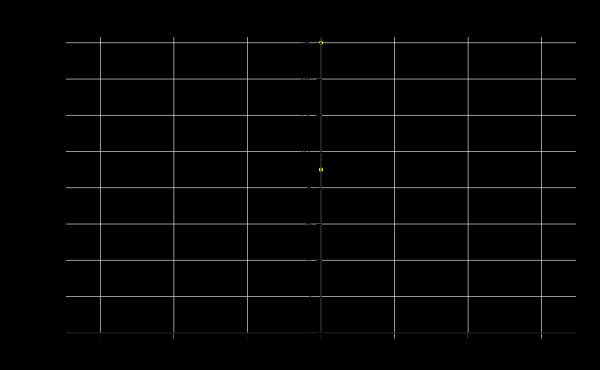
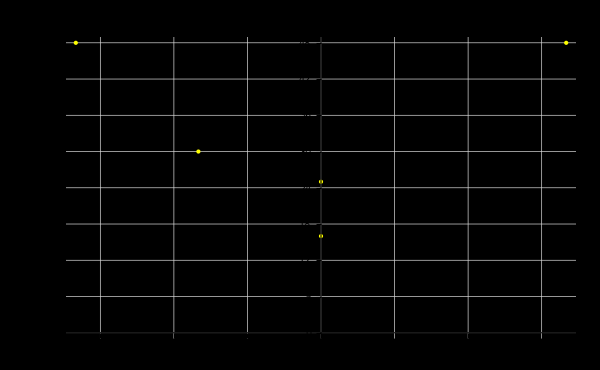
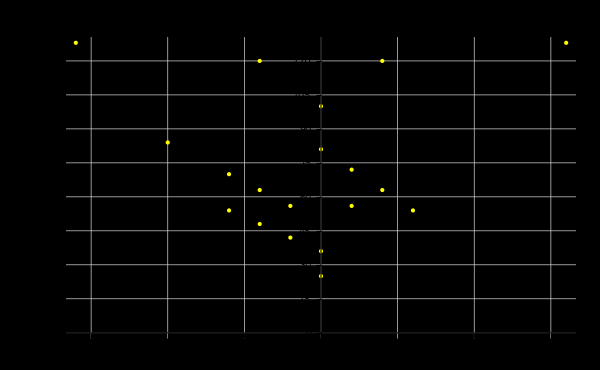
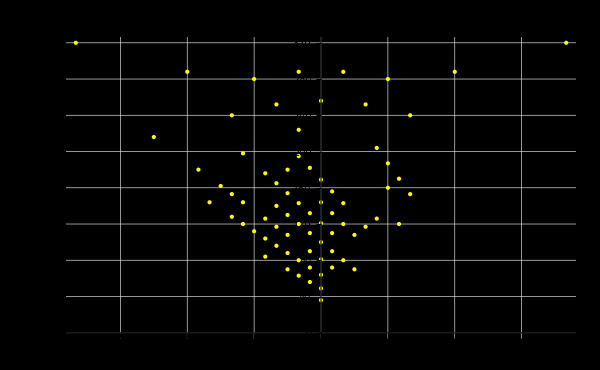
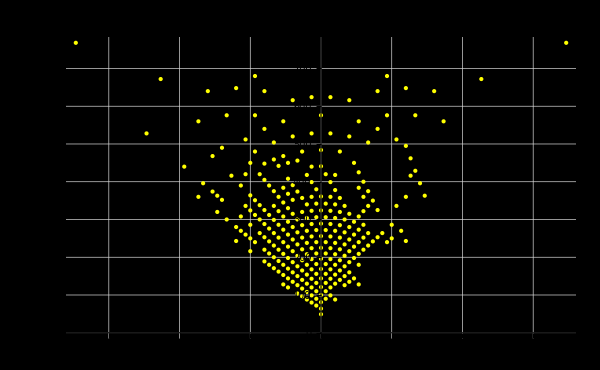
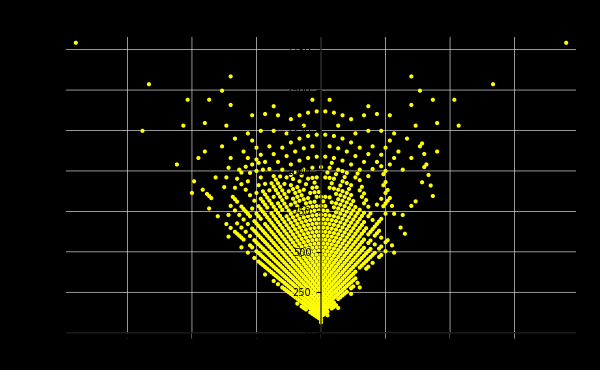
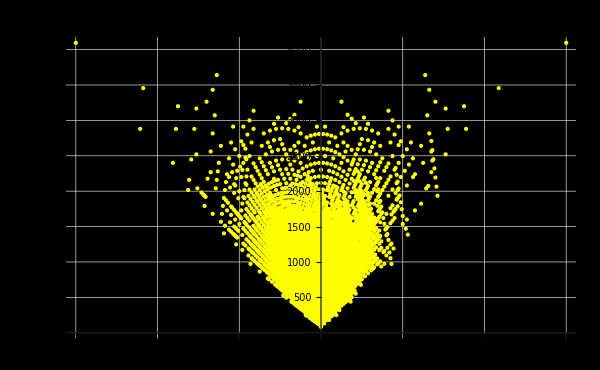
{-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{pt[[1]]-pt[[2]],Times@@pt},pt])/@#1,PlotRange->All,PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Difference vs Product in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"f·v"}],Style["f-v",White,Background->Black],Background->Black]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-dif-prod-plot-"<>ToString[#2[[1]]]<>".jpg"}],#1,Background->Black]&,%];
```

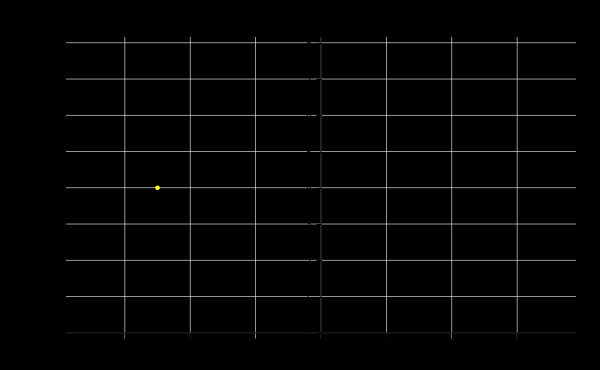
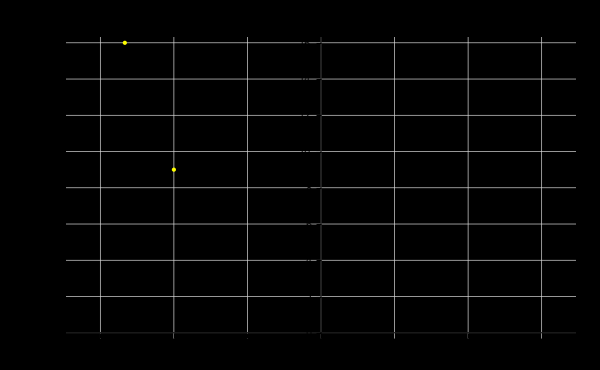
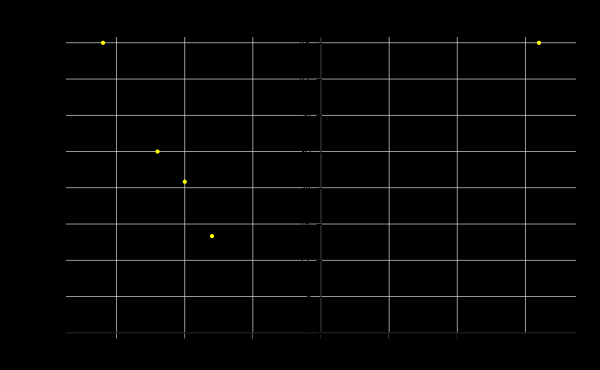
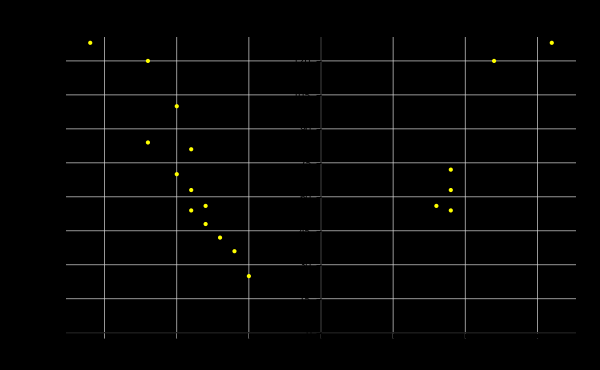
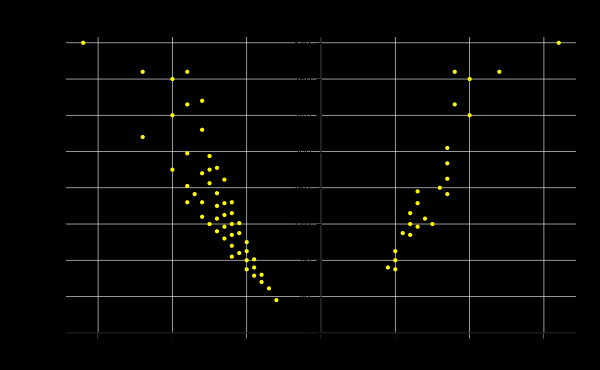
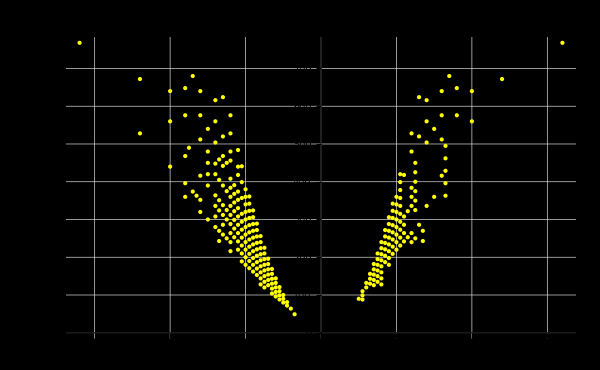
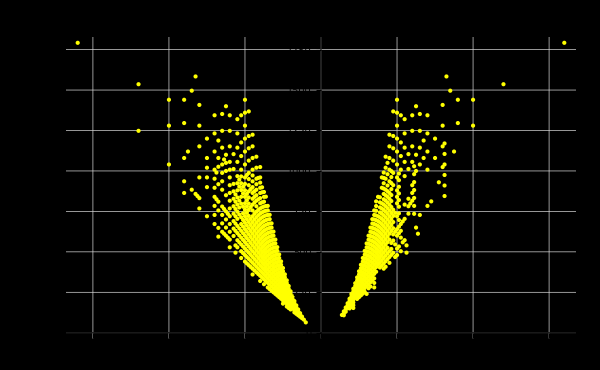
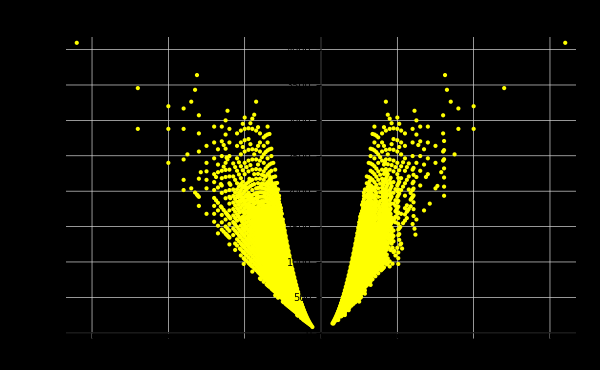
{-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v)}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{If[pt[[1]]>pt[[2]],pt[[1]],-pt[[2]]],Times@@pt},pt])/@#1,PlotRange->{{-2^(#2[[1]])-1,2^(#2[[1]])+1},All},PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Max vs Product in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"f·v"}],Style["(-1)^(f > v)max(f,v)",White,Background->Black],Background->Black]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-max-prod-plot-"<>ToString[#2[[1]]]<>".jpg"}],#1,Background->Black]&,%];
```

```mathematica
peculiarSzs=<|4->{{8,16},{10,12}(*?*)},5->{{10,32},{16,18}},6->{{12,64},{20,34},{24,26}(*?*)},7->{{14,128},{24,66},{36,40}},8->{{16,256},{28,130},{48,68}}|>;
```

```mathematica
{2(#-0),2^#}&/@{4,5,6,7,8}
```

{{8,16},{10,32},{12,64},{14,128},{16,256}}

```mathematica
{4(#-1),2^(#-1)+2}&/@{5,6,7,8}
```

{{16,18},{20,34},{24,66},{28,130}}

```mathematica
{24,26}(*?*),{36,40},{48,68}
```

```mathematica
{12(#-4),2^(#-2)+4}&/@{6,7,8}
```

{{24,20},{36,36},{48,68}}

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rawData1to7=Import[FileNameJoin[{"data",ToString[#]}]]&/@Range[7];
```

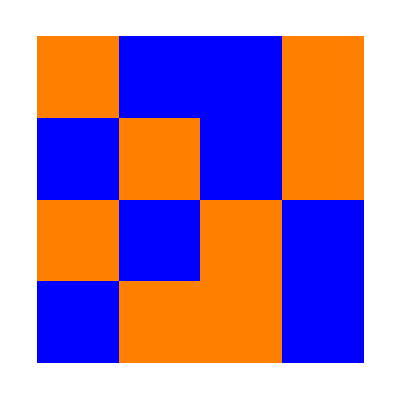
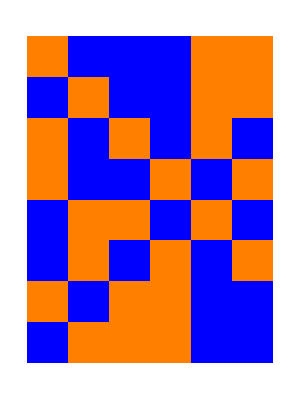
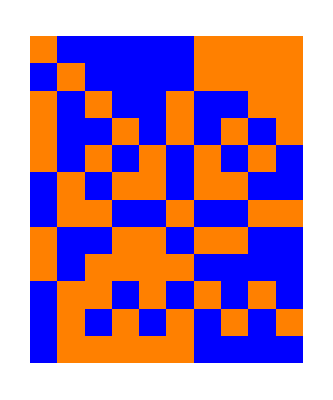
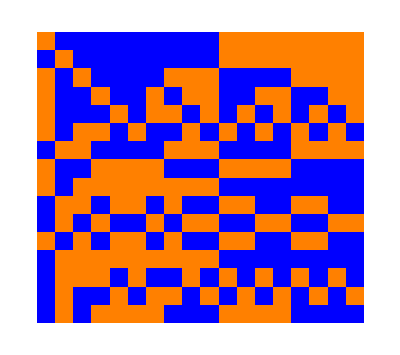
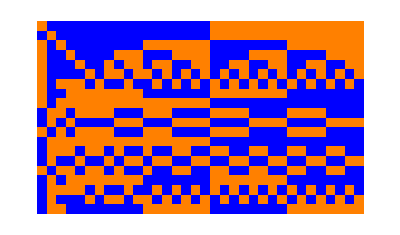
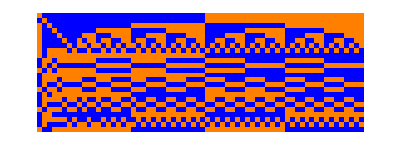

```mathematica
pecSecond=Table[ArrayPlot[Partition[IntegerDigits[Select[rawData1to7[[d]],#[[3;;4]]=={4(d-1),2^(d-1)+2}&][[1,-1]]],2^(d-1)+2],ColorRules->{1->Orange,0->Blue},Frame->False],{d,2,7}]
```

```mathematica
{4(#-1),2^(#-1)+2}&/@Range[8]
```

{{0,3},{4,4},{8,6},{12,10},{16,18},{20,34},{24,66},{28,130}}

Transformation of (presumably centrally symmetric) polytopes to 0-1 vectors

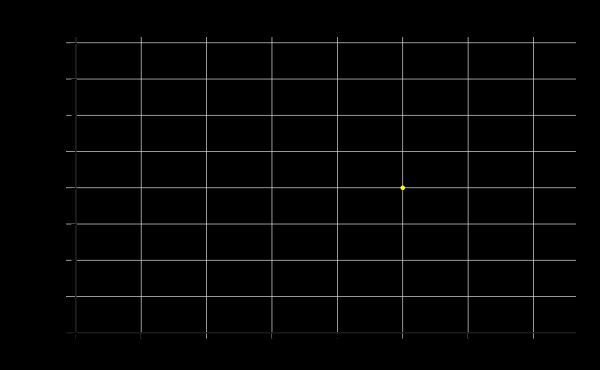
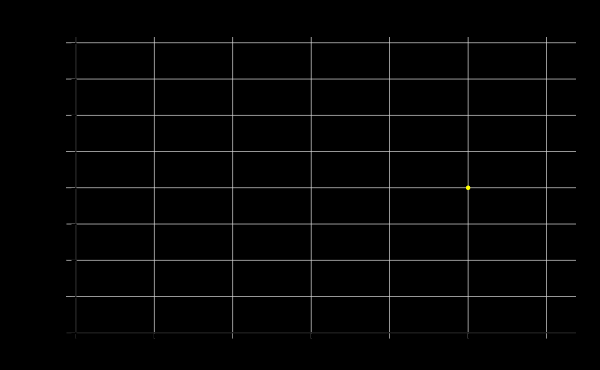
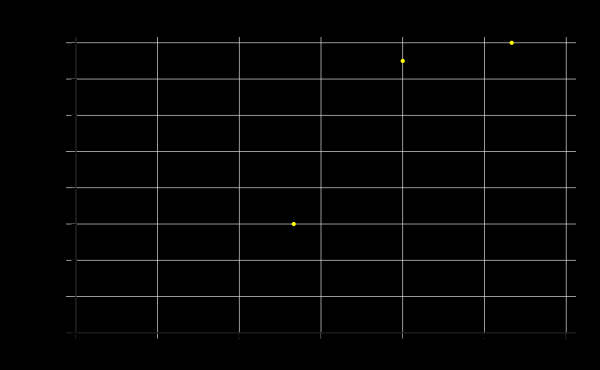
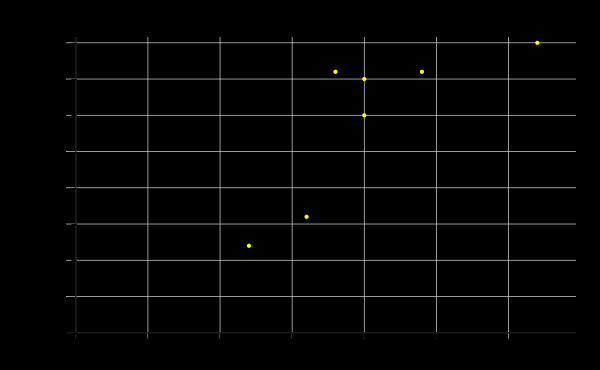
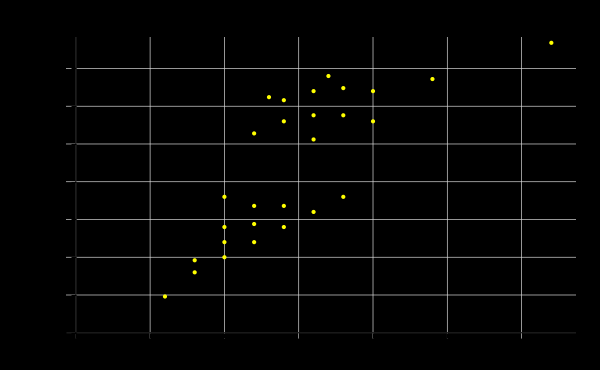
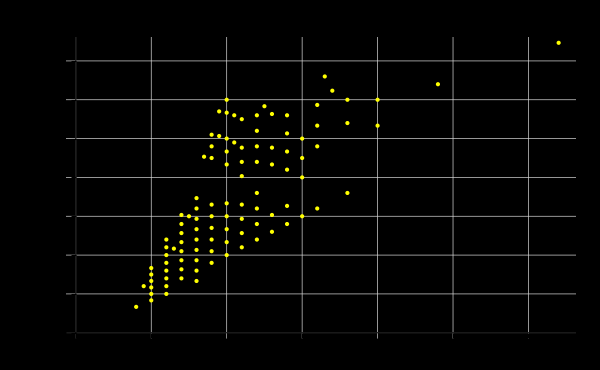
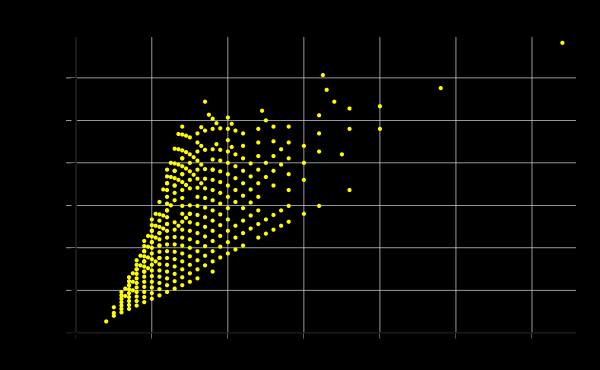
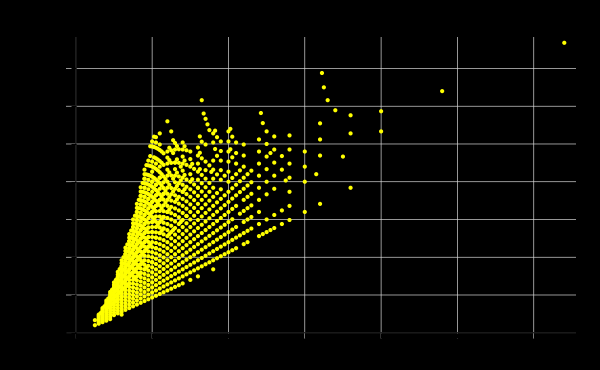
{-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2)}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{Max@pt,Times@@pt},pt])/@#1,PlotRange->{{0,2^(#2[[1]])+1},All},PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Max vs Product for families arising from even polytopes in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"a_1·a_2"}],Style["max(a_1,a_2)",White,Background->Black],Background->Black]&,Map[If[And@@EvenQ[#],{(#[[1]])/2+1,#[[2]]},Nothing]&,facetVertData,{2}]]
```

```mathematica
MapIndexed[Export["families-from-even-max-vs-prod-"<>ToString[#2[[1]]]<>".jpg",#1,Background->Black]&,%];
```

```mathematica
Grid[Table[Style[{2^(d-k)+k,2^k(d-k+1)},White,Background->If[2^(d-k)+k>2^k(d-k+1),Red,Blue]],{d,0,11},{k,0,d}],Frame->All,Background->Black,FrameStyle->Gray]
```

{1,1} |  |  |  |  |  |  |  |  |  |  | 
{2,2} | {2,2} |  |  |  |  |  |  |  |  |  | 
{4,3} | {3,4} | {3,4} |  |  |  |  |  |  |  |  | 
{8,4} | {5,6} | {4,8} | {4,8} |  |  |  |  |  |  |  | 
{16,5} | {9,8} | {6,12} | {5,16} | {5,16} |  |  |  |  |  |  | 
{32,6} | {17,10} | {10,16} | {7,24} | {6,32} | {6,32} |  |  |  |  |  | 
{64,7} | {33,12} | {18,20} | {11,32} | {8,48} | {7,64} | {7,64} |  |  |  |  | 
{128,8} | {65,14} | {34,24} | {19,40} | {12,64} | {9,96} | {8,128} | {8,128} |  |  |  | 
{256,9} | {129,16} | {66,28} | {35,48} | {20,80} | {13,128} | {10,192} | {9,256} | {9,256} |  |  | 
{512,10} | {257,18} | {130,32} | {67,56} | {36,96} | {21,160} | {14,256} | {11,384} | {10,512} | {10,512} |  | 
{1024,11} | {513,20} | {258,36} | {131,64} | {68,112} | {37,192} | {22,320} | {15,512} | {12,768} | {11,1024} | {11,1024} | 
{2048,12} | {1025,22} | {514,40} | {259,72} | {132,128} | {69,224} | {38,384} | {23,640} | {16,1024} | {13,1536} | {12,2048} | {12,2048}

```mathematica
Grid[Table[Style[{(2^(d-k)+k)(2^k(d-k+1))},White,Background->If[2^(d-k)+k>2^k(d-k+1),Red,Blue]],{d,0,11},{k,0,d}],Frame->All,Background->Black,FrameStyle->Gray]
```

{1} |  |  |  |  |  |  |  |  |  |  | 
{4} | {4} |  |  |  |  |  |  |  |  |  | 
{12} | {12} | {12} |  |  |  |  |  |  |  |  | 
{32} | {30} | {32} | {32} |  |  |  |  |  |  |  | 
{80} | {72} | {72} | {80} | {80} |  |  |  |  |  |  | 
{192} | {170} | {160} | {168} | {192} | {192} |  |  |  |  |  | 
{448} | {396} | {360} | {352} | {384} | {448} | {448} |  |  |  |  | 
{1024} | {910} | {816} | {760} | {768} | {864} | {1024} | {1024} |  |  |  | 
{2304} | {2064} | {1848} | {1680} | {1600} | {1664} | {1920} | {2304} | {2304} |  |  | 
{5120} | {4626} | {4160} | {3752} | {3456} | {3360} | {3584} | {4224} | {5120} | {5120} |  | 
{11264} | {10260} | {9288} | {8384} | {7616} | {7104} | {7040} | {7680} | {9216} | {11264} | {11264} | 
{24576} | {22550} | {20560} | {18648} | {16896} | {15456} | {14592} | {14720} | {16384} | {19968} | {24576} | {24576}

```mathematica
With[{hypBound=(2^(#1-#2)+#2)2^#2(#1-#2+1)&},hypBound[d,k]-2hypBound[d-1,k]//FullSimplify]
```

2^d+2^k k (1-d+k)

```mathematica
<<"data/facet-vert-data-1to8.mx"
```

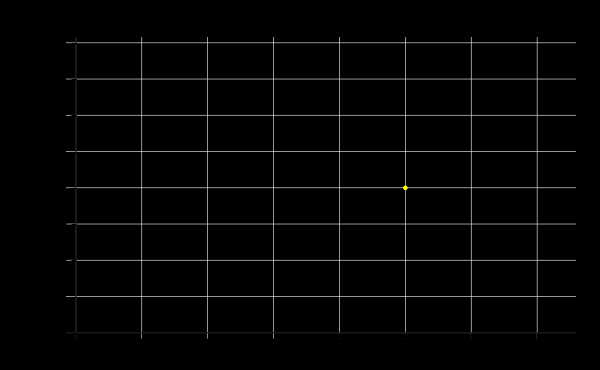
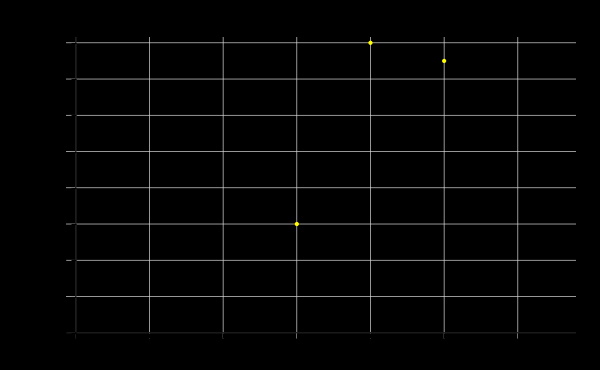
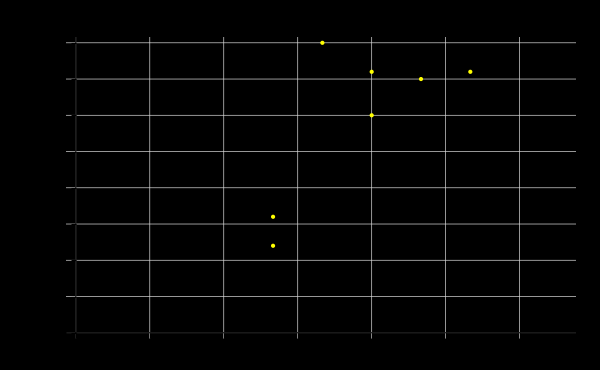
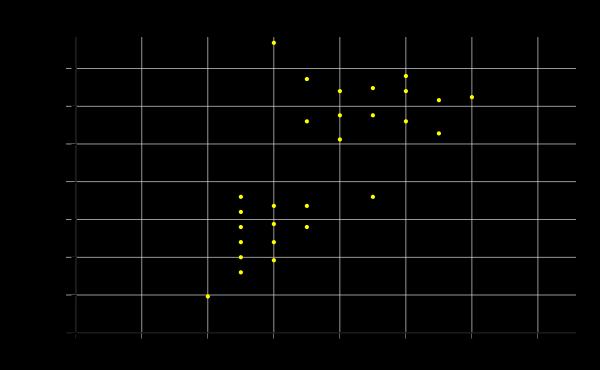
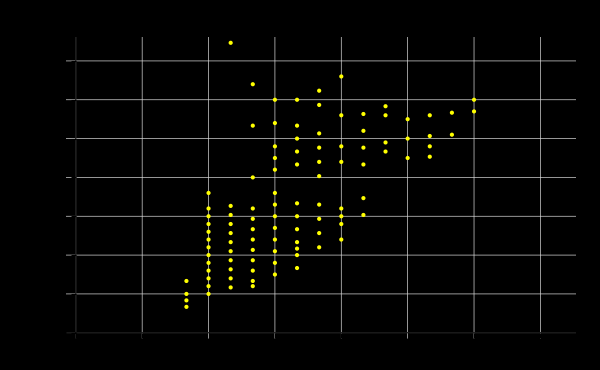
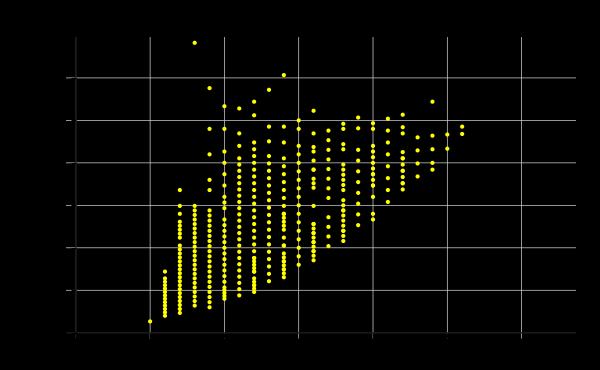
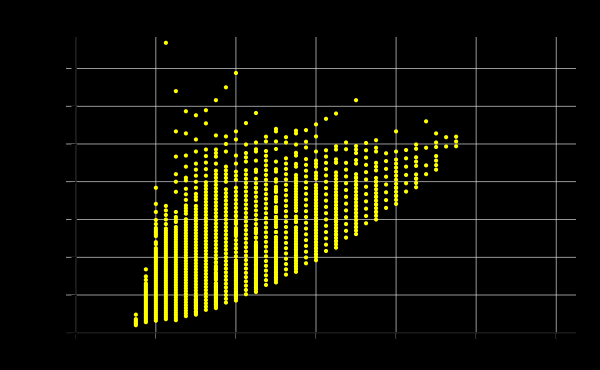
{-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2)}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{Min@pt,Times@@pt},pt])/@#1,PlotRange->{{0,2^((#2[[1]])/2)Sqrt[#2[[1]]+1]+1},All},PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Min vs Product for families arising from even polytopes in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"a_1·a_2"}],Style["min(a_1,a_2)",White,Background->Black],Background->Black]&,Map[If[And@@EvenQ[#],{(#[[1]])/2+1,#[[2]]},Nothing]&,facetVertData,{2}]]
```

```mathematica
MapIndexed[Export["families-from-even-min-vs-prod-"<>ToString[#2[[1]]]<>".jpg",#1,Background->Black]&,%];
```

```mathematica
2^k(d-k+1)(2^(d-k)+k)-(2^k(d-k+1)+2^k(d-k)(2^(d-k-1)+k)+2^(d-1)d)//FullSimplify
```

-2^k (1+d-2 k)-2^(-1+d) (-2+k)

```mathematica
2^k(d-k+1)(2^(d-k)+k)-(2^k(d-k+1)+2^(k-1)(d-k+1)(2^(d-k)+k-1)+2^(κ-1)(d-κ)(2^(d-κ-1)+κ))//FullSimplify
```

-1/2 (2^d+2^k (-1+k)) (1+d-k)+2^k (-1-d+k)+(1+d-k) (2^d+2^k k)+1/4 (-d+κ) (2^d+2^(1+κ) κ)

Trying a subexact bound:

```mathematica
2^d(d-k+2)-(2^k(d-k+1)+2^(d-1)(d-k+1)+d 2^(d-1))//FullSimplify
```

-2^(-1+d) (-3+k)+2^k (-1-d+k)

```mathematica
Assuming[{k∈PositiveIntegers,d∈PositiveIntegers},Sum[t 2^(t-1),{t,1,d}]]
```

1-2^d+2^d d

```mathematica
Assuming[{k∈PositiveIntegers,d∈PositiveIntegers},Sum[t 2^(t-1),{t,1,d-k}]]
```

2^-k (-2^d+2^k+2^d d-2^d k)

```mathematica
Sum[t 2^(t-1),{t,d-k+1,d}]
```

2^(d-k) (1-2^k-d+2^k d+k)

```mathematica
FullSimplify[(d-k+1)2^(d-k)+Sum[t 2^(t-1),{t,d-k+1,d}]+(d-k+1)(2^(k+1)-2),Assumptions->{k∈PositiveIntegers,d∈PositiveIntegers}]
```

-2-2^d+2^(1+d-k)-2 d+2^d d+2^(1+k) (1+d-k)+2 k

```mathematica
2^k(d-k+1)(2^(d-k)+k)-((d-k+1)2^(d-k)+Sum[t 2^(t-1),{t,d-k+1,d}]+(d-k+1)(2^(k+1)-2))//FullSimplify
```

-2^-k (2+2^k (-2+k)) (2^d+2^k (-1-d+k))

```mathematica
((d-k+1)2^(d-k)+Sum[t 2^(t-1),{t,d-k+1,d}]+(d-k+1)(2^(k+1)-2))-2^k(d-k+1)(2^(d-k)+k)//FullSimplify
```

2^-k (2+2^k (-2+k)) (2^d+2^k (-1-d+k))

```mathematica
potenBound[d_,k_]:=2^d(d-1)+2^(d-k+1)+(2^(k+1)-2)(d-k+1)
```

```mathematica
(potenBound[d,k]-2^(d+1)-2^(d-U)potenBound[U,k+d-U]/.U->1)//FullSimplify
```

-2+2^(1-k) (-2+2^d)-2 d-(-2+2^d) k+2^(-1+k) (4 (1+d-k)+4^d (-3+d+k))

```mathematica
With[{u=5},{expr=(potenBound[d,k]-2^(d+1)-2^(d-u)potenBound[u,k-(d-u)])},Grid[Table[With[{val=(expr/.{d->dd,k->kk})},Style[N[val,1],White,Background->If[dd>u,If[val>=0,RGBColor[0.06, 0.42, 0.],RGBColor[1, 0, 0]],If[val>=0,RGBColor[0.06, 0.42, 0.],RGBColor[0.35000000000000003, 0, 0]]]]],{dd,1,12},{kk,0,dd}],Frame->All,FrameStyle->Gray,Background->Black]](*☹️*)
```

-10. | -10. |  |  |  |  |  |  |  |  |  |  | 
-20. | -20. | -20. |  |  |  |  |  |  |  |  |  | 
-30. | -30. | -30. | -30. |  |  |  |  |  |  |  |  | 
-40. | -40. | -50. | -50. | -50. |  |  |  |  |  |  |  | 
-60. | -60. | -60. | -60. | -60. | -60. |  |  |  |  |  |  | 
-200. | -100. | -90. | -70. | -70. | -60. | -60. |  |  |  |  |  | 
-700. | -300. | -200. | -70. | -20. | -6. | 0 | 0 |  |  |  |  | 
-3000. | -1000. | -500. | -100. | 100. | 200. | 200. | 300. | 300. |  |  |  | 
-10000. | -6000. | -3000. | -700. | 200. | 700. | 900. | 1000. | 1000. | 1000. |  |  | 
-60000. | -30000. | -10000. | -4000. | -500. | 1000. | 2000. | 3000. | 3000. | 3000. | 3000. |  | 
-200000. | -100000. | -60000. | -20000. | -7000. | 1000. | 5000. | 7000. | 8000. | 8000. | 8000. | 8000. | 
-1.×10^6 | -500000. | -200000. | -100000. | -40000. | -10000. | 6000. | 10000. | 20000. | 20000. | 20000. | 20000. | 20000.

```mathematica
With[{b=IdentityMatrix[3]},Graphics3D[{Arrow[{{0,0,0},{0,0,1}+#}]&/@Join[b,-#&/@b],Red,Arrow[{{0,0,0},1/2(#+{0,0,1})}]&/@(b[[1;;2]]ᵀ.#&/@Tuples[{1,-1},2])}]]
```

-Graphics3D-

```mathematica
With[{expr=potenBound[d,k]-(2(2^k(d-k))(2^(d-k-1)+k)+2^k(2^(d-k)))},Grid[Table[Style[expr,White,Background->If[expr>=0,RGBColor[0.06, 0.42, 0.],If[2^(d-k)+k>2^k(d-k+1),RGBColor[1, 0, 0],RGBColor[0.53, 0., 0., 0.81]]]],{d,1,13},{k,0,d}],Frame->All,Background->Black]]
```

0 | 2 |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 8 |  |  |  |  |  |  |  |  |  |  | 
0 | -2 | 0 | 24 |  |  |  |  |  |  |  |  |  | 
0 | -4 | -6 | 0 | 64 |  |  |  |  |  |  |  |  | 
0 | -6 | -8 | -14 | 0 | 160 |  |  |  |  |  |  |  | 
0 | -8 | -2 | -8 | -30 | 0 | 384 |  |  |  |  |  |  | 
0 | -10 | 20 | 38 | 8 | -62 | 0 | 896 |  |  |  |  |  | 
0 | -12 | 74 | 164 | 182 | 72 | -126 | 0 | 2048 |  |  |  |  | 
0 | -14 | 192 | 450 | 628 | 598 | 264 | -254 | 0 | 4608 |  |  |  | 
0 | -16 | 438 | 1056 | 1618 | 1908 | 1686 | 776 | -510 | 0 | 10240 |  |  | 
0 | -18 | 940 | 2302 | 3696 | 4786 | 5172 | 4374 | 2056 | -1022 | 0 | 22528 |  | 
0 | -20 | 1954 | 4828 | 7950 | 10800 | 12786 | 13108 | 10774 | 5128 | -2046 | 0 | 49152 | 
0 | -22 | 3992 | 9914 | 16556 | 23086 | 28656 | 32114 | 31796 | 25622 | 12296 | -4094 | 0 | 106496

```mathematica
potenBound[d-1,k-1]+2^k(d-k+1)+d 2^(d-1)-potenBound[d,k]//FullSimplify
```

0

```mathematica
2^k(d-k+1)+(2^k-2)(d-k+2)-(2^(k+1)-2)(d-k+1)//FullSimplify
```

-2+2^k

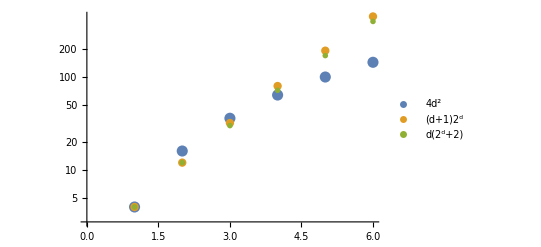

```mathematica
ListLogPlot[Table[{4 d^2,(d+1)2^d,d(2^d+2)},{d,1,6}]ᵀ,PlotLegends->{"4d^2","(d+1)2^d","d(2^d+2)"},PlotStyle->(PointSize/@{0.02,0.015,0.01})]
```

```mathematica
Grid[Table[Table[Style[(d+k)(2^(d-k)+2^(d-1)),White,Background->If[(d+k)(2^(d-k)+2^(d-1))<=2d(2^(d-1)+1),RGBColor[0.07, 0.5, 0.5],RGBColor[1, 0, 0]]],{k,1,d}],{d,1,12}],Frame->All,Background->Black,FrameStyle->Gray]
```

4 |  |  |  |  |  |  |  |  |  |  | 
12 | 12 |  |  |  |  |  |  |  |  |  | 
32 | 30 | 30 |  |  |  |  |  |  |  |  | 
80 | 72 | 70 | 72 |  |  |  |  |  |  |  | 
192 | 168 | 160 | 162 | 170 |  |  |  |  |  |  | 
448 | 384 | 360 | 360 | 374 | 396 |  |  |  |  |  | 
1024 | 864 | 800 | 792 | 816 | 858 | 910 |  |  |  |  | 
2304 | 1920 | 1760 | 1728 | 1768 | 1848 | 1950 | 2064 |  |  |  | 
5120 | 4224 | 3840 | 3744 | 3808 | 3960 | 4160 | 4386 | 4626 |  |  | 
11264 | 9216 | 8320 | 8064 | 8160 | 8448 | 8840 | 9288 | 9766 | 10260 |  | 
24576 | 19968 | 17920 | 17280 | 17408 | 17952 | 18720 | 19608 | 20560 | 21546 | 22550 | 
53248 | 43008 | 38400 | 36864 | 36992 | 38016 | 39520 | 41280 | 43176 | 45144 | 47150 | 49176

```mathematica
2(d-2)(2^(d-1)+4)+2^(d+1)-2d(2^(d-1)+1)//FullSimplify
```

-16+6 d

```mathematica
2*4(d-2)(2^(d-3)+2)+2^d-(2d(2^(d-1)+1))//FullSimplify
```

-32-2^d+14 d

```mathematica
2d(2^(d-1)+1)-2*2(d-1)(2^(d-2)+1)//FullSimplify
```

4+2^d-2 d

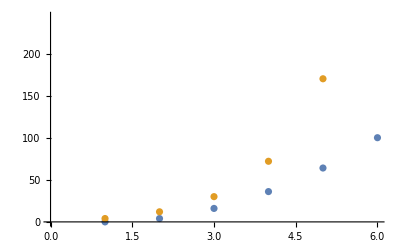

```mathematica
ListPlot[Table[{4(d-1)^2,d 2^d+2d},{d,1,6}]ᵀ]
```

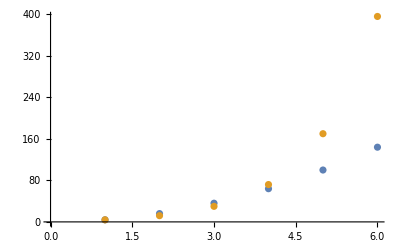

```mathematica
ListPlot[Table[{4 d^2,d 2^d+2d},{d,1,6}]ᵀ]
```

```mathematica
2d(2^(d-1)+1)+2d-4-(2(2(d-1)(2^(d-2)+1))+2^d)//FullSimplify
```

0

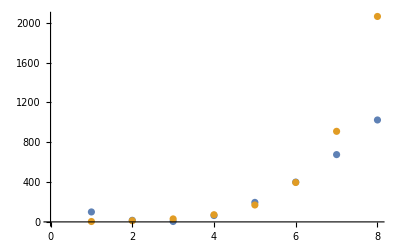

```mathematica
ListPlot[Table[{4(3d-8)^2,d 2^d+2d},{d,1,8}]ᵀ]
```

```mathematica
{4(3d-8)^2,d 2^d+2d}/.d->3
```

{4,30}